# Obtaining the escape energy function from the basin plots

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new

Here we obtain the escape energy function from the basin plots in “BasinPlots.nb” (or “WeakMagField2new.nb”). We obtain the escape energy function in the form of data points (ρ_0,ε(ρ_0)). The data are located in “E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData”

```mathematica
ρmin[b_]:=Module[{r,minr},
If[$IsPositive,minr=r/.First@NSolve[b-(√2(3-r)^(1/2))/(2r(4 r^2-9r+3+√((3r-1)(3-r)))^(1/2))==0,r,Reals],minr=r/.First@NSolve[b-(√2(3-r)^(1/2))/(2r(4 r^2-9r+3-√((3r-1)(3-r)))^(1/2))==0,r,Reals]];
Return[minr]
];
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black};pixels=500;
```

For all the basin plots, the maximum ρ is set to 5. We label the axis in divisions of 10.

```mathematica
ρRange=5;labelDivision=10;
```

We employ the WadaMergingMethod Package and use some of its functionalities.

```mathematica
Needs["WadaMergingMethod`"]
```

You can read about the package in

```mathematica
$UserBaseDirectory
```

C:\Users\Joshua\AppData\Roaming\Mathematica

## Basin plots in the (ρ_0,ε) plane

## Positive l

```mathematica
$IsPositive=True;
εRange={0,3};
```

### b=0.1

```mathematica
Basin=Import["b01pl500.mx"];
b=0.1;
Regionε = Subdivide[εRange⟦2⟧,εRange⟦1⟧,pixels];Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
ε1Location=Ceiling[(εRange⟦2⟧-1)/((εRange⟦2⟧-εRange⟦1⟧)/pixels)];
yLabels=Append[Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}],{ε1Location,"1.00"}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
```

```mathematica
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
```

```mathematica
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
```

```mathematica
Dimensions[slimB]
```

{4,501,501}

```mathematica
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->800],{i,1,4}]]
```

-Graphics-

We take the first plot and use that to obtain the escape energy

```mathematica
slimB=slimB⟦1⟧;
MatrixPlot[slimB,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->800]
```

-Graphics-

We do this by checking each pixel of the basin if the pixel nearby and above it is white. If not, then we remove that pixel.

```mathematica
tempMat=slimB;
```

```mathematica
For[i=2,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-20,1];;i-1,j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->800]
```

-Graphics-

```mathematica
escB=tempMat;
```

Next, we obtain the positions of the remaining black pixels

```mathematica
escPos=Position[escB,1];
```

```mathematica
escPos⟦1⟧
```

{295,1}

Each entry in escPos is an ordered pair {yPos, xPos}, and the data point {ε,ρ} corresponding to that should be {Regionε⟦yPos⟧, Regionρ0⟦xPos⟧}

```mathematica
{Regionε⟦295⟧,Regionρ0⟦1⟧}//N
```

{1.236,2.34833}

We obtain the data points by threading the positions escPos to the corresponding {Regionε⟦yPos⟧, Regionρ0⟦xPos⟧}:

```mathematica
size=Length[escPos]
```

501

```mathematica
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
```

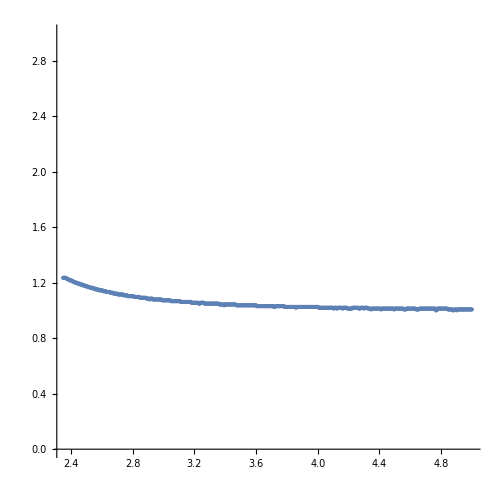

```mathematica
ListPlot[escData,PlotRange-> {All,{0,3}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

We have now obtained data points for the escape energy function (ρ_0,ε(ρ_0)) for the given b=0.1.

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b01plescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b01plescEdat.mx

### b=0.2

```mathematica
Basin=Import["b02pl500.mx"];
b=0.2;
Regionε=Subdivide[3,0,pixels];Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
```

```mathematica
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
```

```mathematica
For[i=2,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;i-1,j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

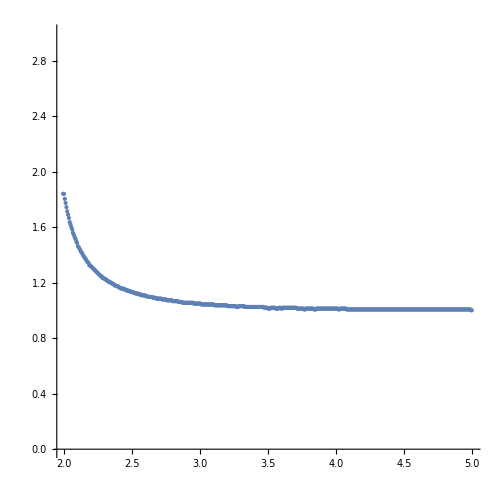

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {All,{0,3}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b02plescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b02plescEdat.mx

### b=0.3

```mathematica
Basin=Import["b03pl500.mx"];
b=0.3;
Regionε=Subdivide[3,0,pixels];Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],Min[j+1,size];;Min[j+50,size]⟧,1,2],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

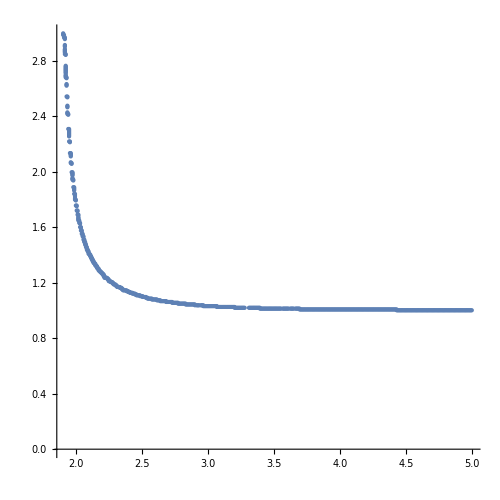

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {All,{0,3}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b03plescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b03plescEdat.mx

### b=0.4

```mathematica
Basin=Import["b04pl500.mx"];
b=0.4;
Regionε=Subdivide[3,0,pixels];Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],Min[j+1,size];;Min[j+50,size]⟧,1,2],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

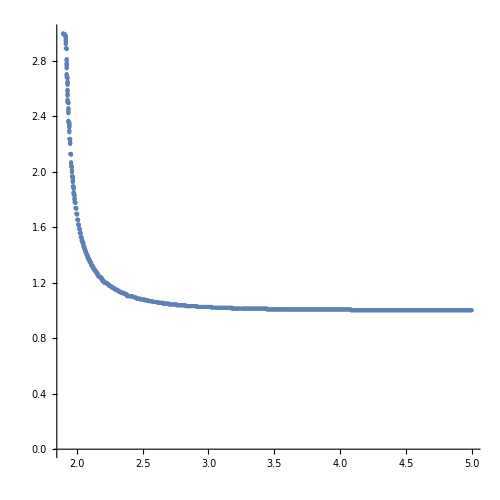

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {All,{0,3}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b04plescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b04plescEdat.mx

### b=0.5

```mathematica
Basin=Import["b05pl500.mx"];
b=0.5;
Regionε=Subdivide[3,0,pixels];Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],Min[j+1,size];;Min[j+50,size]⟧,1,2],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

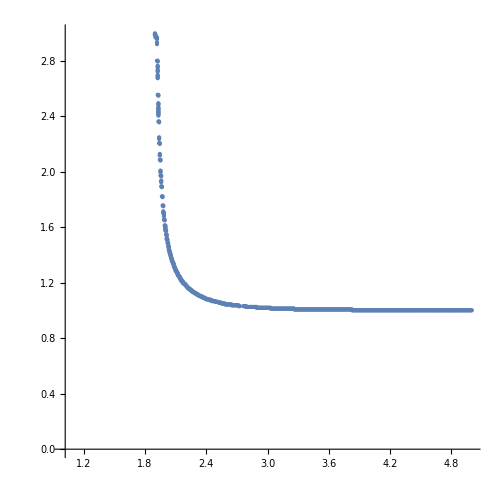

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {{1,5},{0,3}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b05plescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b05plescEdat.mx

## Negative l

```mathematica
$IsPositive=False;
εRange={1,6};
Regionε = Subdivide[εRange⟦2⟧,εRange⟦1⟧,pixels];
ε1Location=Ceiling[(εRange⟦2⟧-1)/((εRange⟦2⟧-εRange⟦1⟧)/pixels)];
```

### b=0.1

```mathematica
Basin=Import["b01ml500.mx"];
b=0.1;
Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

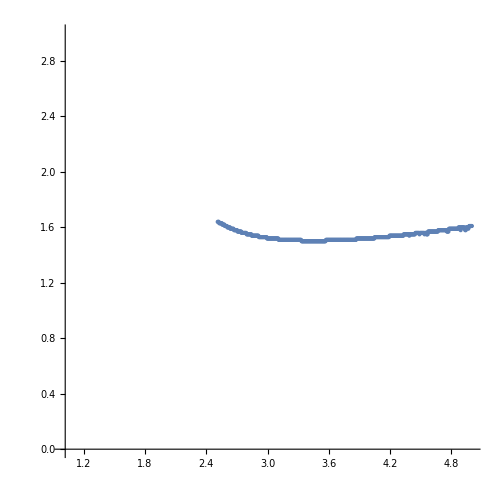

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {{1,5},{0,3}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b01mlescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b01mlescEdat.mx

### b=0.2

```mathematica
Basin=Import["b02ml500.mx"];
b=0.2;
Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

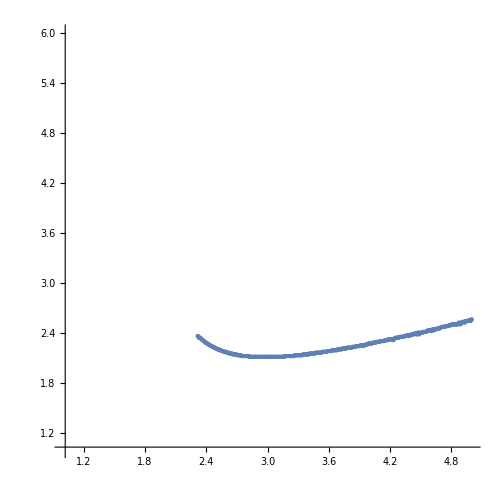

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {{1,5},{1,6}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b02mlescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b02mlescEdat.mx

### b=0.3

```mathematica
Basin=Import["b03ml500.mx"];
b=0.3;
Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

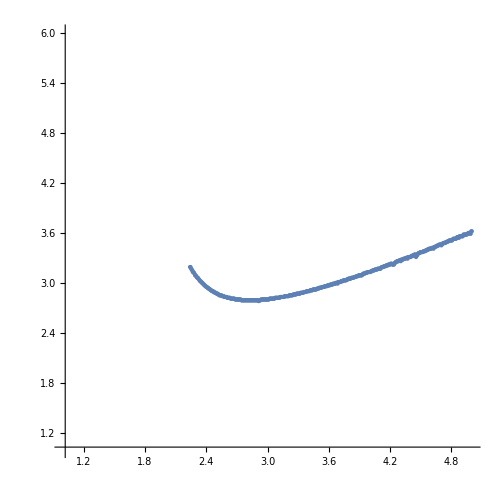

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {{1,5},{1,6}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b03mlescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b03mlescEdat.mx

### b=0.4

```mathematica
Basin=Import["b04ml500.mx"];
b=0.4;
Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

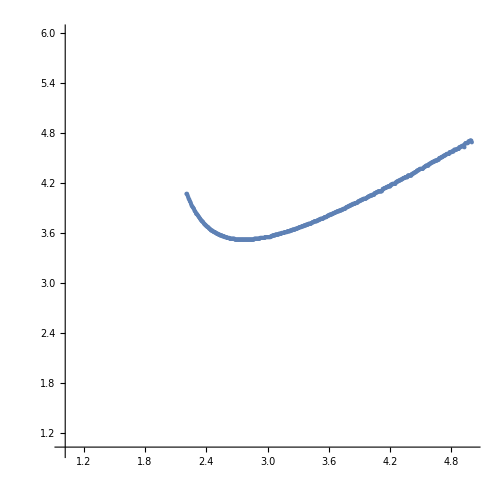

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {{1,5},{1,6}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b04mlescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b04mlescEdat.mx

### b=0.5

```mathematica
Basin=Import["b05ml500.mx"];
b=0.5;
Regionρ0 = Subdivide[Evaluate[ρmin[b]],ρRange,pixels];
yLabels=Table[{i,N[Round[Regionε⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
xLabels=Table[{i,N[Round[Regionρ0⟦i⟧,10^-2],3]},{i,1,pixels+1,Floor[(pixels+1)/labelDivision]}];
BasinPlot=MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{yLabels,xLabels},PlotLabel->"b="<>ToString[b],MaxPlotPoints->Infinity];
Show[BasinPlot,ImageSize->500,BaseStyle->{FontSize->14},LabelStyle->{FontSize->14}]
```

-Graphics-

```mathematica
slimB=getSlimBoundaries[Basin];
GraphicsRow[Table[MatrixPlot[slimB⟦i⟧,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->500],{i,1,4}]]
```

-Graphics-

```mathematica
slimB=slimB⟦1⟧;
```

```mathematica
tempMat=slimB;
size=First@Dimensions[slimB];
For[i=1,i≤size,i++,
For[j=1,j≤size,j++,
If[MemberQ[slimB⟦Max[i-50,1];;Max[i-1,1],j⟧,1],tempMat⟦i⟧⟦j⟧=0]
]
]
```

```mathematica
MatrixPlot[tempMat,ColorRules->{0->White,1->Black},FrameTicks->{yLabels,xLabels},MaxPlotPoints->Infinity,ImageSize->600]
```

-Graphics-

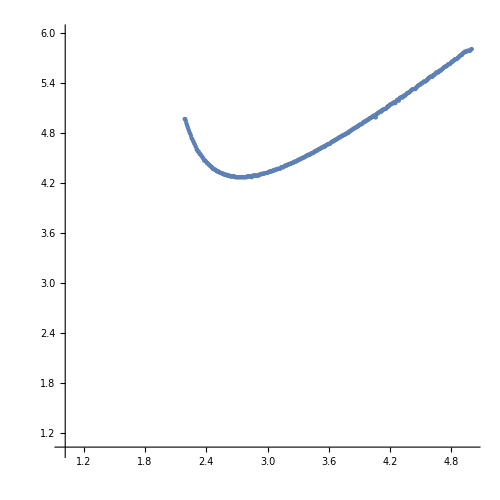

```mathematica
escB=tempMat;
escPos=Position[escB,1];
size=Length[escPos];
escData=Table[{Regionρ0⟦Last@escPos⟦i⟧⟧,Regionε⟦First@escPos⟦i⟧⟧},{i,1,size}];
ListPlot[escData,PlotRange-> {{1,5},{1,6}},AspectRatio->1,ImageSize->500,PlotStyle->PointSize[Small]]
```

```mathematica
Export["E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\b05mlescEdat.mx",escData]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\b05mlescEdat.mx